D:\VELA\GIT Projects\Software\Apps\RF_Conditioner\logs\data

```mathematica
typemap=<|"<enum 'ramp_method'>"->"Byte","<type 'numpy.float64'>"->"Integer64","<type 'numpy.float64'>"->"Real64","<enum 'state'>"->"Byte", "<class 'VELA_CLARA_enums.STATE'>"->"Byte","<class 'VELA_CLARA_RF_Modulator_Control.GUN_MOD_STATE'>"->"Byte","<class 'VELA_CLARA_RF_Protection_Control.RF_GUN_PROT_STATUS'>"->"Byte","<class 'VELA_CLARA_Vac_Valve_Control.VALVE_STATE'>"->"Byte","<type 'bool'>"->"Byte","<type 'float'>"->"Real32","<type 'int'>"->"Integer32","<type 'long'>"->"Integer32","<class 'VELA_CLARA_LLRF_Control.TRIG'>"->"Byte"
,"<class 'VELA_CLARA_enums.STATE'>"->"Byte","<class 'VELA_CLARA_RF_Modulator_Control.GUN_MOD_STATE'>"->"Byte",
"<class 'VELA_CLARA_LLRF_Control.INTERLOCK_STATE'>"->"Byte","<class 'VELA_CLARA_LLRF_Control.TRIG'>"->"Byte","<class 'VELA_CLARA_RF_Protection_Control.RF_PROT_STATUS'>"->"Byte","<class 'VELA_CLARA_RF_Protection_Control.RF_GUN_PROT_STATUS'>"->"Byte","<class 'VELA_CLARA_Vac_Valve_Control.VALVE_STATE'>"->"Byte","<type 'bool'>"->"Byte","<type 'float'>"->"Real32","<type 'int'>"->"Integer32","<type 'long'>"->"Integer32","<enum 'state'>"->"Byte"|>;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\djs56\GitHub\Software\Apps\RF_Conditioner\v2\data_log_reader

```mathematica
FileNames[]
```

{2020-08-04-13-51-54,data_log,data_log_read_multifile_20200804.nb}

```mathematica
file="data_log";
str=OpenRead[file,BinaryFormat->True];
heads=StringSplit[ReadLine[str],"\t"]
types=StringSplit[ReadLine[str],"\t"]
BinaryRead[str,{"Character8"}]
data=BinaryReadList[str,Lookup[typemap,types]]
Close[str]
```

{p0_all,llrf_output_status,next_sp_decrease,probe_pha,rev_cav_pha,can_llrf_output_state_OLD,breakdown_rate_aim,phi_sp,num_outside_mask_traces,next_requested_power_change,modulator_good,p2_current_sp_to_fit,CAVITY_TEMP_ID_0,p2_current_sp,pulse_length_status,pulse_length,llrf_trace_interlock,cav_pwr_ratio_good,llrf_interlock,SP_QUAD_ALL,water_temp_gui,last_requested_power_change,max_sp_increase,ramp_mode,llrf_ff_ph_locked,rev_kly_pha,llrf_ff_amp_locked_status,pulse_length_min,llrf_DAQ_rep_rate_status_previous,delta_kfpow,llrf_trigger,cav_pwr_ratio_can_ramp,p1_current_sp_to_fit,vac_level,gui_can_rf_output,can_rf_output_status_OLD,bd_rate_calc_first_pulse_number,pulse_length_max,cav_pwr_ratio,number_of_pulses_in_breakdown_history,probe_outside_mask_count,llrf_interlock_status,current_ramp_index,y_min,old_x_min,old_x_max,rev_kly_pwr,fwd_kly_pha,active_breakdown_count,last_sp_above_100,event_pulse_count,time_stamp, (start = 2020-08-04 13:52:18.463000),log_ramp_curve_index,TOR_SCAN,llrf_ff_ph_locked_status,last_mean_power,rev_cav_pwr,SP_QUAD_CURRENT_SP_TO_FIT,last_vac_spike_status,llrf_DAQ_rep_rate_status,x_max,p0_current_sp_to_fit,amp_ff,c,L01-SOL1,L01-SOL2,y_max,p1_current_sp,x_min,can_ramp_status,kfpower_at_last_amp_sp,vac_level_can_ramp,last_breakdown_status,reverse_outside_mask_count,llrf_DAQ_rep_rate_min,llrf_DAQ_rep_rate_max,TOR_ACQM,p0_current_sp,breakdown_rate_low,WATER_TEMP_ID_1,cav_temp,fwd_cav_pha,BD_state_OLD,rfprot_good,last_amp_sp,vac_spike_status,old_y_max,event_pulse_count_zero,DC_level,amp_sp,global_mask_checking,gui_can_ramp,can_llrf_output_state,p1_all,expected_pulse_length,old_y_min,log_pulse_count,llrf_DAQ_rep_rate_aim,llrf_ff_amp_locked,catap_max_amp,can_ramp_status_OLD,p2_all,fwd_kly_pwr,sol_value,log_amp_set,duplicate_pulse_count,m,pulse_count,fwd_cav_pwr,SP_SLF,WATER_TEMP_ID_0,probe_pwr,llrf_output,can_rf_output_status,log_pulse_length,modulator_state,elapsed_time,DC_spike_status,llrf_trigger_status,pulses_to_next_ramp,GUI_mod_and_prot_good,breakdown_status,catap_max_amp_can_ramp_status,main_can_ramp,llrf_DAQ_rep_rate,vac_valve_status,SP_QUAD_CURRENT,rev_power_spike_count,BD_state,last_ramp_method,required_pulses,rfprot_state,old_m,total_breakdown_count,old_c,cav_temp_gui}

{<type 'numpy.float64'>,<enum 'state'>,<type 'float'>,<type 'float'>,<type 'float'>,<enum 'state'>,<type 'int'>,<type 'int'>,<type 'int'>,<type 'int'>,<type 'bool'>,<type 'numpy.float64'>,<type 'float'>,<type 'numpy.float64'>,<enum 'state'>,<type 'int'>,<type 'bool'>,<type 'bool'>,<class 'VELA_CLARA_LLRF_Control.INTERLOCK_STATE'>,<type 'float'>,<type 'float'>,<type 'int'>,<type 'float'>,<enum 'ramp_method'>,<type 'bool'>,<type 'float'>,<enum 'state'>,<type 'int'>,<enum 'state'>,<type 'float'>,<class 'VELA_CLARA_LLRF_Control.TRIG'>,<type 'bool'>,<type 'numpy.float64'>,<type 'float'>,<type 'bool'>,<enum 'state'>,<type 'int'>,<type 'int'>,<type 'float'>,<type 'int'>,<type 'int'>,<enum 'state'>,<type 'int'>,<type 'numpy.float64'>,<type 'float'>,<type 'float'>,<type 'float'>,<type 'float'>,<type 'int'>,<type 'float'>,<type 'int'>,<type 'float'>,<type 'int'>,<type 'int'>,<enum 'state'>,<type 'float'>,<type 'float'>,<type 'float'>,<enum 'state'>,<enum 'state'>,<type 'float'>,<type 'numpy.float64'>,<type 'int'>,<type 'numpy.float64'>,<type 'float'>,<type 'float'>,<type 'numpy.float64'>,<type 'numpy.float64'>,<type 'float'>,<enum 'state'>,<type 'float'>,<type 'bool'>,<enum 'state'>,<type 'int'>,<type 'int'>,<type 'int'>,<type 'int'>,<type 'numpy.float64'>,<type 'bool'>,<type 'float'>,<type 'float'>,<type 'float'>,<enum 'state'>,<type 'bool'>,<type 'float'>,<enum 'state'>,<type 'numpy.float64'>,<type 'int'>,<type 'float'>,<type 'float'>,<type 'bool'>,<type 'bool'>,<enum 'state'>,<type 'numpy.float64'>,<type 'int'>,<type 'numpy.float64'>,<type 'int'>,<type 'int'>,<type 'bool'>,<type 'float'>,<enum 'state'>,<type 'numpy.float64'>,<type 'float'>,<type 'float'>,<type 'int'>,<type 'int'>,<type 'numpy.float64'>,<type 'int'>,<type 'float'>,<type 'float'>,<type 'float'>,<type 'float'>,<type 'bool'>,<enum 'state'>,<type 'float'>,<class 'VELA_CLARA_RF_Modulator_Control.GUN_MOD_STATE'>,<type 'long'>,<enum 'state'>,<enum 'state'>,<type 'int'>,<type 'bool'>,<enum 'state'>,<type 'bool'>,<type 'bool'>,<type 'float'>,<class 'VELA_CLARA_Vac_Valve_Control.VALVE_STATE'>,<type 'float'>,<type 'int'>,<enum 'state'>,<enum 'ramp_method'>,<type 'int'>,<class 'VELA_CLARA_RF_Protection_Control.RF_PROT_STATUS'>,<type 'numpy.float64'>,<type 'int'>,<type 'numpy.float64'>,<type 'float'>}

{\r}

{1}
 |  |  |  |

data_log

```mathematica
data⟦1⟧
```

{-2.16172×10^17,192,6.35275×10^-22,6.35285×10^-22,-3.26794×10^22,66,25602,-4864,255,1734967552,255,-2.16172×10^17,6.35284×10^-22,-2.16172×10^17,192,638209,0,1,0,6.35275×10^-22,-8.79636×10^36,1734967617,6.35288×10^-22,198,13,-4.36828×10^23,19,160563523,0,0.0000829715,37,71,-3.78425×10^-270,4.94412×10^28,20,48,1472135681,167182327,1.43597×10^-30,1078115338,-2130702526,105,570556263,Indeterminate,1.77026×10^-38,1.81936×10^-38,5.76577×10^-9,1.40648×10^-37,4396954,0.,12983360,0.,-2117723072,50292585,0,9.18355×10^-41,-1.86302×10^-35,5.88228×10^-39,64,28,9.28304×10^-41,Indeterminate,-2118073465,Indeterminate,-4.7726×10^29,-4.86452×10^29,Indeterminate,Indeterminate,1.77026×10^-38,64,2.54739×10^-40,64,28,-2130574906,134178665,218103808,33554432,Indeterminate,135,6.39732×10^-30,6.06026×10^-39,-1.47604×10^-6,237,52,9.26468×10^-41,64,Indeterminate,-4144249,2.36679×10^-42,1.81936×10^-38,0,0,0,Indeterminate,-993999993,Indeterminate,-4144249,218105497,10,2.35099×10^-38,0,-6.27173×10^292,-6.11035,1.22392,-971227136,3021,-6.27173×10^292,-1060927489,6.06256×10^-40,2.35,-10000.,31.6034,0,64,9.53428×10^-38,150,222104387,237,153,24361351,0,0,2,1,-3.07599×10^38,0,-2.46527×10^-32,21045546,0,64,1770112540,103,1.24335729×10^-314,-54975581,1.59782797×10^-314,-7.69038×10^36}

## Concatenating Data Logs

```mathematica
FastListPlot[data_,opts:OptionsPattern[]]:=Module[{interp},interp=Interpolation[data];
Plot[interp[x],{x,interp[[1,1,1]],interp[[1,1,2]]},opts]]
```

```mathematica
getDataLog[fn_]:=Block[{file=fn,str,heads,types,data,typemap=<|"<class 'VELA_CLARA_enums.STATE'>"->"Byte","<class 'VELA_CLARA_RF_Modulator_Control.GUN_MOD_STATE'>"->"Byte",
"<class 'VELA_CLARA_LLRF_Control.INTERLOCK_STATE'>"->"Byte","<class 'VELA_CLARA_LLRF_Control.TRIG'>"->"Byte","<class 'VELA_CLARA_RF_Protection_Control.RF_PROT_STATUS'>"->"Byte","<class 'VELA_CLARA_RF_Protection_Control.RF_GUN_PROT_STATUS'>"->"Byte","<class 'VELA_CLARA_Vac_Valve_Control.VALVE_STATE'>"->"Byte","<type 'bool'>"->"Byte","<type 'float'>"->"Real32","<type 'int'>"->"Integer32","<type 'long'>"->"Integer32","<enum 'state'>"->"Byte"|>,data2,timestamp,ts},
str=OpenRead[file,BinaryFormat->True];
heads=StringSplit[ReadLine[str],"\t"];
types=StringSplit[ReadLine[str],"\t"];
BinaryRead[str,{"Character8"}];
data=BinaryReadList[str,Lookup[typemap,types]];
Close[str];
data2=data;
(* Now we offset the timestamp column to be in seconds since the epoch... *)
timestamp=Position[StringContainsQ[heads,"time_stamp"],True];
ts=AbsoluteTime[DateObject[StringTake[Extract[heads,timestamp]⟦1⟧,{22,-4}]]];
data2⟦All,timestamp⟦1⟧⟧=Flatten[data2⟦All,timestamp⟦1⟧⟧+ts];
{heads,data2}
]
```

## many files

```mathematica
directoryroot="C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\Breakdowns";
SetDirectory[directoryroot];
datadirs=Select[FileNames[],DirectoryQ@#&]
```

{Binary_log,ML,outside_forward,outside_reverse}

SetDirectory::cdir: Cannot set current directory to C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\Breakdowns\Binary_log\data_log.

{ABViewer 14,AllTraces,Appraisals,AP_RF_Lecture_notes,Bead_Pull,Cern,Cockroft Institute Lectures,Covid-19,CST,Custom Office Templates,ESS,Git,GPC,gun_10_csv_data,Gun_10_Upgrade,High Power RF Test Area,Induction,IPAC,Mathematica,Mechanical_Drawings,MSc JBCA,OneNote Notebooks,Oracle,Papers,Study Material,Training,USPAS,Wolfram Mathematica,XFEL,Zoom}

```mathematica
(*get folders adn files that contain this string *)
lfstring=".dat";
datafiles=FileNameJoin[{directoryroot,#⟦1⟧,#⟦2,1⟧}]&/@Select[Table[
SetDirectory[FileNameJoin[{directoryroot,datadirs⟦i⟧}]];
{datadirs⟦i⟧,Select[FileNames[],StringContainsQ[#,lfstring]&]}
,{i,1,Length@datadirs}],Length@#⟦2⟧>0&];
```

SetDirectory::cdir: Cannot set current directory to C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\Breakdowns\Binary_log\data_log\ABViewer 14.

SetDirectory::cdir: Cannot set current directory to C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\Breakdowns\Binary_log\data_log\AllTraces.

SetDirectory::cdir: Cannot set current directory to C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\Breakdowns\Binary_log\data_log\Appraisals.

General::stop: Further output of SetDirectory::cdir will be suppressed during this calculation.

```mathematica
Speak[lfstring=".dat";]
```

```mathematica
td=getDataLog[#]&/@datafiles;
```

```mathematica
Transpose[{td⟦1,1⟧,Range@Length@td⟦1,1⟧}]
```

{{llrf_DAQ_rep_rate_min,1},{phi_sp,2},{x_max,3},{next_sp_decrease,4},{probe_pha,5},{rev_cav_pha,6},{llrf_DAQ_rep_rate_max,7},{TOR_ACQM,8},{breakdown_rate_aim,9},{llrf_output_status,10},{num_outside_mask_traces,11},{cav_temp,12},{fwd_cav_pha,13},{pulse_length_status,14},{pulse_length,15},{llrf_interlock,16},{last_106_bd_count,17},{pulse_length_aim,18},{breakdown_rate_hi,19},{amp_sp,20},{PID_on_off,21},{max_sp_increase,22},{old_y_max,23},{llrf_ff_ph_locked,24},{rev_kly_pha,25},{vac_val_limit,26},{breakdown_rate,27},{vac_spike_status,28},{next_power_increase,29},{water_temp,30},{pulse_length_min,31},{vac_valve_status,32},{pulse_length_aim_error,33},{llrf_trigger_status,34},{log_pulse_count,35},{llrf_trigger,36},{llrf_DAQ_rep_rate_aim,37},{power_aim,38},{vac_level,39},{llrf_DAQ_rep_rate_status_previous,40},{phase_mask_by_power_trace_2_set,41},{y_min,42},{rev_power_spike_count,43},{phase_end_mask_by_power_trace_2_time,44},{fwd_kly_pwr,45},{breakdown_count,46},{probe_pwr,47},{log_amp_set,48},{duplicate_pulse_count,49},{pulse_length_max,50},{phase_mask_by_power_trace_1_set,51},{pulse_count,52},{fwd_cav_pwr,53},{llrf_ff_amp_locked_status,54},{sol_value,55},{llrf_output,56},{DC_level,57},{llrf_interlock_status,58},{current_ramp_index,59},{log_pulse_length,60},{old_x_min,61},{modulator_state,62},{llrf_ff_amp_locked,63},{old_x_max,64},{phase_end_mask_by_power_trace_1_time,65},{elapsed_time,66},{rev_kly_pwr,67},{DC_spike_status,68},{fwd_kly_pha,69},{last_sp_above_100,70},{event_pulse_count,71},{time_stamp, (start = 2019-12-04 17:50:42.185000),72},{TOR_SCAN,73},{llrf_ff_ph_locked_status,74},{last_mean_power,75},{rev_cav_pwr,76},{x_min,77},{old_y_min,78},{llrf_DAQ_rep_rate_status,79},{can_rf_output,80},{llrf_DAQ_rep_rate,81},{c,82},{y_max,83},{m,84},{breakdown_status,85},{required_pulses,86},{rfprot_state,87},{old_m,88},{old_c,89},{can_rf_output_OLD,90}}

```mathematica
{{"llrf_DAQ_rep_rate_min",1},{"phi_sp",2},{"x_max",3},{"next_sp_decrease",4},{"probe_pha",5},{"rev_cav_pha",6},{"llrf_DAQ_rep_rate_max",7},{"TOR_ACQM",8},{"breakdown_rate_aim",9},{"llrf_output_status",10},{"num_outside_mask_traces",11},{"cav_temp",12},{"fwd_cav_pha",13},{"pulse_length_status",14},{"pulse_length",15},{"llrf_interlock",16},{"last_106_bd_count",17},{"pulse_length_aim",18},{"breakdown_rate_hi",19},{"amp_sp",20},{"PID_on_off",21},{"max_sp_increase",22},{"old_y_max",23},{"llrf_ff_ph_locked",24},{"rev_kly_pha",25},{"vac_val_limit",26},{"breakdown_rate",27},{"vac_spike_status",28},{"next_power_increase",29},{"water_temp",30},{"pulse_length_min",31},{"vac_valve_status",32},{"pulse_length_aim_error",33},{"llrf_trigger_status",34},{"log_pulse_count",35},{"llrf_trigger",36},{"llrf_DAQ_rep_rate_aim",37},{"power_aim",38},{"vac_level",39},{"llrf_DAQ_rep_rate_status_previous",40},{"phase_mask_by_power_trace_2_set",41},{"y_min",42},{"rev_power_spike_count",43},{"phase_end_mask_by_power_trace_2_time",44},{"fwd_kly_pwr",45},{"breakdown_count",46},{"probe_pwr",47},{"log_amp_set",48},{"duplicate_pulse_count",49},{"pulse_length_max",50},{"phase_mask_by_power_trace_1_set",51},{"pulse_count",52},{"fwd_cav_pwr",53},{"llrf_ff_amp_locked_status",54},{"sol_value",55},{"llrf_output",56},{"DC_level",57},{"llrf_interlock_status",58},{"current_ramp_index",59},{"log_pulse_length",60},{"old_x_min",61},{"modulator_state",62},{"llrf_ff_amp_locked",63},{"old_x_max",64},{"phase_end_mask_by_power_trace_1_time",65},{"elapsed_time",66},{"rev_kly_pwr",67},{"DC_spike_status",68},{"fwd_kly_pha",69},{"last_sp_above_100",70},{"event_pulse_count",71},{"time_stamp, (start = 2019-12-04 17:50:42.185000)",72},{"TOR_SCAN",73},{"llrf_ff_ph_locked_status",74},{"last_mean_power",75},{"rev_cav_pwr",76},{"x_min",77},{"old_y_min",78},{"llrf_DAQ_rep_rate_status",79},{"can_rf_output",80},{"llrf_DAQ_rep_rate",81},{"c",82},{"y_max",83},{"m",84},{"breakdown_status",85},{"required_pulses",86},{"rfprot_state",87},{"old_m",88},{"old_c",89},{"can_rf_output_OLD",90}}


DuplicatePulseCount=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,49⟧}],{i,1,Length@td}]],2];
DuplicatePulseCount0=Transpose[{DuplicatePulseCount⟦All,1⟧-DuplicatePulseCount⟦1,1⟧,DuplicatePulseCount⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\DuplicatePulseCount_Data.csv",DuplicatePulseCount0,"Table"]
```

{{llrf_DAQ_rep_rate_min,1},{phi_sp,2},{x_max,3},{next_sp_decrease,4},{probe_pha,5},{rev_cav_pha,6},{llrf_DAQ_rep_rate_max,7},{TOR_ACQM,8},{breakdown_rate_aim,9},{llrf_output_status,10},{num_outside_mask_traces,11},{cav_temp,12},{fwd_cav_pha,13},{pulse_length_status,14},{pulse_length,15},{llrf_interlock,16},{last_106_bd_count,17},{pulse_length_aim,18},{breakdown_rate_hi,19},{amp_sp,20},{PID_on_off,21},{max_sp_increase,22},{old_y_max,23},{llrf_ff_ph_locked,24},{rev_kly_pha,25},{vac_val_limit,26},{breakdown_rate,27},{vac_spike_status,28},{next_power_increase,29},{water_temp,30},{pulse_length_min,31},{vac_valve_status,32},{pulse_length_aim_error,33},{llrf_trigger_status,34},{log_pulse_count,35},{llrf_trigger,36},{llrf_DAQ_rep_rate_aim,37},{power_aim,38},{vac_level,39},{llrf_DAQ_rep_rate_status_previous,40},{phase_mask_by_power_trace_2_set,41},{y_min,42},{rev_power_spike_count,43},{phase_end_mask_by_power_trace_2_time,44},{fwd_kly_pwr,45},{breakdown_count,46},{probe_pwr,47},{log_amp_set,48},{duplicate_pulse_count,49},{pulse_length_max,50},{phase_mask_by_power_trace_1_set,51},{pulse_count,52},{fwd_cav_pwr,53},{llrf_ff_amp_locked_status,54},{sol_value,55},{llrf_output,56},{DC_level,57},{llrf_interlock_status,58},{current_ramp_index,59},{log_pulse_length,60},{old_x_min,61},{modulator_state,62},{llrf_ff_amp_locked,63},{old_x_max,64},{phase_end_mask_by_power_trace_1_time,65},{elapsed_time,66},{rev_kly_pwr,67},{DC_spike_status,68},{fwd_kly_pha,69},{last_sp_above_100,70},{event_pulse_count,71},{time_stamp, (start = 2019-12-04 17:50:42.185000),72},{TOR_SCAN,73},{llrf_ff_ph_locked_status,74},{last_mean_power,75},{rev_cav_pwr,76},{x_min,77},{old_y_min,78},{llrf_DAQ_rep_rate_status,79},{can_rf_output,80},{llrf_DAQ_rep_rate,81},{c,82},{y_max,83},{m,84},{breakdown_status,85},{required_pulses,86},{rfprot_state,87},{old_m,88},{old_c,89},{can_rf_output_OLD,90}}

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\DuplicatePulseCount_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\DuplicatePulseCount_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\DuplicatePulseCount_Data.csv

```mathematica
probepha=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,5⟧}],{i,1,Length@td}]],2];
probepha0=Transpose[{probepha⟦All,1⟧-probepha⟦1,1⟧,probepha⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\probepha_Data.csv",probepha0,"Table"]

BreakdownCount=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,46⟧}],{i,1,Length@td}]],2];
BreakdownCount0=Transpose[{BreakdownCount⟦All,1⟧-BreakdownCount⟦1,1⟧,BreakdownCount⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\BreakdownCount_Data.csv",BreakdownCount0,"Table"]

PulseCount=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,52⟧}],{i,1,Length@td}]],2];
PulseCount0=Transpose[{PulseCount⟦All,1⟧-PulseCount⟦1,1⟧,PulseCount⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\PulseCount_Data.csv",PulseCount0,"Table"]
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\probepha_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\BreakdownCount_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\PulseCount_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\probepha_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\probepha_Data.csv

```mathematica
RevCavPha=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,6⟧}],{i,1,Length@td}]],2];
RevCavPha0=Transpose[{RevCavPha⟦All,1⟧-RevCavPha⟦1,1⟧,RevCavPha⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevCavPha_Data.csv",RevCavPha0,"Table"]

NumOutsideMaskTraces=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,11⟧}],{i,1,Length@td}]],2];
NumOutsideMaskTraces0=Transpose[{NumOutsideMaskTraces⟦All,1⟧-NumOutsideMaskTraces⟦1,1⟧,NumOutsideMaskTraces⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\NumOutsideMaskTraces_Data.csv",NumOutsideMaskTraces0,"Table"]

CavTemp=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,12⟧}],{i,1,Length@td}]],2];
CavTemp0=Transpose[{CavTemp⟦All,1⟧-CavTemp⟦1,1⟧,CavTemp⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\CavTemp_Data.csv",CavTemp0,"Table"]

FwdCavPha=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,13⟧}],{i,1,Length@td}]],2];
FwdCavPha0=Transpose[{FwdCavPha⟦All,1⟧-FwdCavPha⟦1,1⟧,FwdCavPha⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\FwdCavPha_Data.csv",FwdCavPha0,"Table"]

PulseLength=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,15⟧}],{i,1,Length@td}]],2];
PulseLength0=Transpose[{PulseLength⟦All,1⟧-PulseLength⟦1,1⟧,PulseLength⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\PulseLength_Data.csv",PulseLength0,"Table"]

RevKlyPha=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,25⟧}],{i,1,Length@td}]],2];
RevKlyPha0=Transpose[{RevKlyPha⟦All,1⟧-RevKlyPha⟦1,1⟧,RevKlyPha⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevKlyPha_Data.csv",RevKlyPha0,"Table"]

BreakdownRate=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,27⟧}],{i,1,Length@td}]],2];
BreakdownRate0=Transpose[{BreakdownRate⟦All,1⟧-BreakdownRate⟦1,1⟧,BreakdownRate⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\BreakdownRate_Data.csv",BreakdownRate0,"Table"]

WaterTemp=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,30⟧}],{i,1,Length@td}]],2];
WaterTemp0=Transpose[{WaterTemp⟦All,1⟧-WaterTemp⟦1,1⟧,WaterTemp⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\WaterTemp_Data.csv",WaterTemp0,"Table"]

LogPulseCount=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,35⟧}],{i,1,Length@td}]],2];
LogPulseCount0=Transpose[{LogPulseCount⟦All,1⟧-LogPulseCount⟦1,1⟧,LogPulseCount⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\LogPulseCount_Data.csv",LogPulseCount0,"Table"]

vacdata=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,39⟧}],{i,1,Length@td}]],2];
vacdata0=Transpose[{vacdata⟦All,1⟧-vacdata⟦1,1⟧,vacdata⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\VAC_Data.csv",vacdata0,"Table"]

kfpdata=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,45⟧}],{i,1,Length@td}]],2];
kfpdata0=Transpose[{kfpdata⟦All,1⟧-kfpdata⟦1,1⟧,kfpdata⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\KFP_Data.csv",kfpdata0,"Table"]


ProbePower=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,47⟧}],{i,1,Length@td}]],2];
ProbePower0=Transpose[{ProbePower⟦All,1⟧-ProbePower⟦1,1⟧,ProbePower⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ProbePower_Data.csv",ProbePower0,"Table"]
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevCavPha_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\NumOutsideMaskTraces_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\CavTemp_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\FwdCavPha_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\PulseLength_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevKlyPha_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\BreakdownRate_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\WaterTemp_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\LogPulseCount_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\VAC_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\KFP_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ProbePower_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevCavPha_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevCavPha_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\NumOutsideMaskTraces_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\NumOutsideMaskTraces_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\CavTemp_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\CavTemp_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\FwdCavPha_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\FwdCavPha_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\PulseLength_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\PulseLength_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevKlyPha_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevKlyPha_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\BreakdownRate_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\BreakdownRate_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\WaterTemp_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\WaterTemp_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\LogPulseCount_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\LogPulseCount_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\VAC_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\VAC_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\KFP_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\KFP_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\BreakdownCount_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\BreakdownCount_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ProbePower_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ProbePower_Data.csv

```mathematica
FwdCavPwr=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,53⟧}],{i,1,Length@td}]],2];
FwdCavPwr0=Transpose[{FwdCavPwr⟦All,1⟧-FwdCavPwr⟦1,1⟧,FwdCavPwr⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\FwdCavPwr_Data.csv",FwdCavPwr0,"Table"]

SolValue=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,55⟧}],{i,1,Length@td}]],2];
SolValue0=Transpose[{SolValue⟦All,1⟧-SolValue⟦1,1⟧,SolValue⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\SolValue_Data.csv",SolValue0,"Table"]

LogPulseLength=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,60⟧}],{i,1,Length@td}]],2];
LogPulseLength0=Transpose[{LogPulseLength⟦All,1⟧-LogPulseLength⟦1,1⟧,LogPulseLength⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\LogPulseLength_Data.csv",LogPulseLength0,"Table"]

ModState=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,62⟧}],{i,1,Length@td}]],2];
ModState0=Transpose[{ModState⟦All,1⟧-ModState⟦1,1⟧,ModState⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ModState_Data.csv",ModState0,"Table"]

ModState=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,62⟧}],{i,1,Length@td}]],2];
ModState0=Transpose[{ModState⟦All,1⟧-ModState⟦1,1⟧,ModState⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ModState_Data.csv",ModState0,"Table"]

ElapsedTime=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,66⟧}],{i,1,Length@td}]],2];
ElapsedTime0=Transpose[{ElapsedTime⟦All,1⟧-ElapsedTime⟦1,1⟧,ElapsedTime⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ElapsedTime_Data.csv",ElapsedTime0,"Table"]

RevKlyPwr=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,67⟧}],{i,1,Length@td}]],2];
RevKlyPwr0=Transpose[{RevKlyPwr⟦All,1⟧-RevKlyPwr⟦1,1⟧,RevKlyPwr⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevKlyPwr_Data.csv",RevKlyPwr0,"Table"]

ForKlyPha=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,69⟧}],{i,1,Length@td}]],2];
ForKlyPha0=Transpose[{ForKlyPha⟦All,1⟧-ForKlyPha⟦1,1⟧,ForKlyPha⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ForKlyPha_Data.csv",ForKlyPha0,"Table"]

EventPulseCount=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,71⟧}],{i,1,Length@td}]],2];
EventPulseCount0=Transpose[{EventPulseCount⟦All,1⟧-EventPulseCount⟦1,1⟧,EventPulseCount⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\EventPulseCount_Data.csv",EventPulseCount0,"Table"]
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\FwdCavPwr_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\SolValue_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\LogPulseLength_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ModState_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ModState_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ElapsedTime_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevKlyPwr_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ForKlyPha_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\EventPulseCount_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\PulseCount_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\PulseCount_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\FwdCavPwr_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\FwdCavPwr_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\SolValue_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\SolValue_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\LogPulseLength_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\LogPulseLength_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ModState_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ModState_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ModState_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ModState_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ElapsedTime_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ElapsedTime_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevKlyPwr_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevKlyPwr_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ForKlyPha_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ForKlyPha_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\EventPulseCount_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\EventPulseCount_Data.csv

```mathematica
RevCavPwr=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,76⟧}],{i,1,Length@td}]],2];
RevCavPwr0=Transpose[{RevCavPwr⟦All,1⟧-RevCavPwr⟦1,1⟧,RevCavPwr⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevCavPwr_Data.csv",RevCavPwr0,"Table"]

BreakdownStatus=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,85⟧}],{i,1,Length@td}]],2];
BreakdownStatus0=Transpose[{BreakdownStatus⟦All,1⟧-BreakdownStatus⟦1,1⟧,BreakdownStatus⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\BreakdownStatus_Data.csv",BreakdownStatus0,"Table"]
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevCavPwr_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\BreakdownStatus_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevCavPwr_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevCavPwr_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\BreakdownStatus_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\BreakdownStatus_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CRP_Data.csv

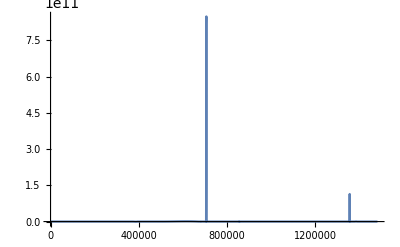

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CRP_Data.csv"
FastListPlot[kfpdata0,PlotRange->All]
```

```mathematica
(* we want time vs vac_level *)
pldata=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,15⟧}],{i,1,Length@td}]],2];
pldata0=Transpose[{pldata⟦All,1⟧-pldata⟦1,1⟧,pldata⟦All,2⟧}];
```

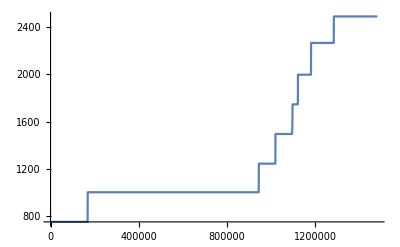

```mathematica
FastListPlot[pldata0,PlotRange->All]
```

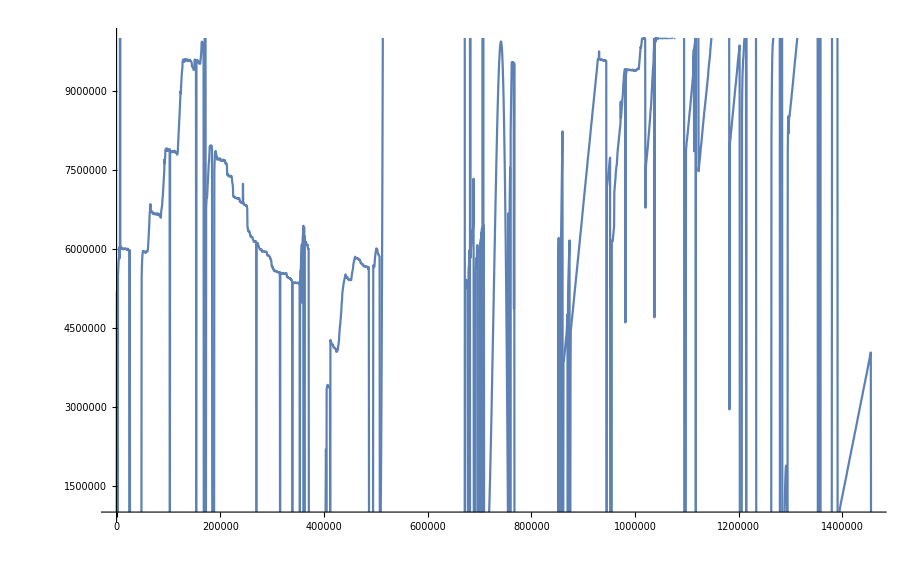

```mathematica
FastListPlot[kfpdata0,PlotRange->{All,{10^6,10^7}}]
```

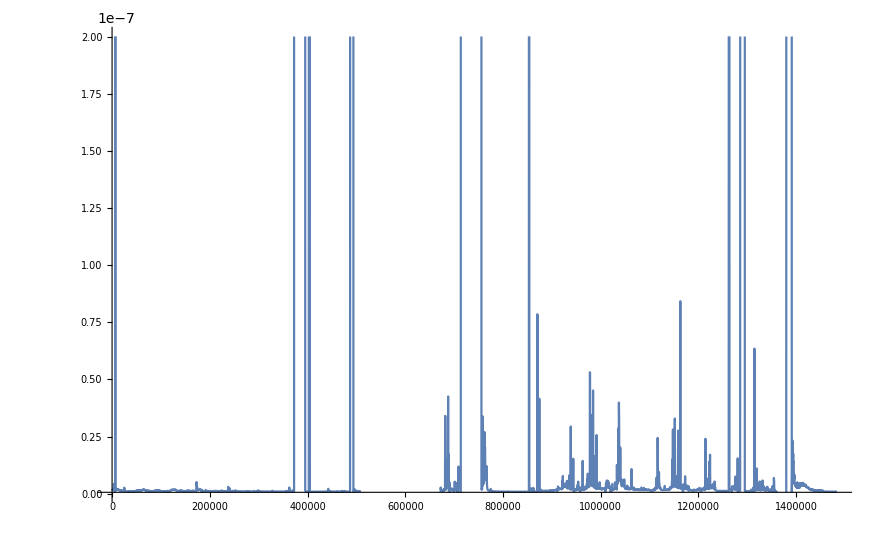

```mathematica
FastListPlot[vacdata0,PlotRange->{All,{6 10^-10,2 10^-7}}]
```

### MultiPlot

```mathematica
ListPlot[vacdata]
```

-Graphics-

```mathematica
dataN=data;
```

```mathematica
P1=ListPlot[dataN⟦All,45⟧,PlotStyle->Blue,ImagePadding->50,Frame->{True,True,True,False},ImageSize->750,FrameStyle->{Automatic,Blue,Automatic,Automatic}];
P2=ListPlot[dataN⟦All,46⟧,PlotStyle->Red,ImagePadding->50,Axes->False,Frame->{False,False,False,True},ImageSize->750,PlotRange->{All,{0,600}},FrameTicks->{{None,All},{None,None}},FrameLabel->{"Time (s)",""},FrameStyle->{Automatic,Automatic,Automatic,Red}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
P3=ListLogPlot[dataN⟦All,39⟧,PlotStyle->Green,ImagePadding->50,Axes->False,Frame->{False,False,False,True},ImageSize->750,PlotRange->{All,{1 10^-10,1 10^-7}},FrameTicks->{{None,All},{None,None}},FrameLabel->{"Time (s)",""},FrameStyle->{Automatic,Automatic,Automatic,Green},Joined->True]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListLogPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

ListLogPlot[Symbol[],PlotStyle→RGBColor[0, 1, 0],ImagePadding→50,Axes→False,Frame→{False,False,False,True},ImageSize→750,PlotRange→{All,{1/10000000000,1/10000000}},FrameTicks→{{None,All},{None,None}},FrameLabel→{Time (s),},FrameStyle→{Automatic,Automatic,Automatic,RGBColor[0, 1, 0]},Joined→True]